## Online supplementary material to SVOČ 2024 thesis

### Mendroš, E. (2024). Bivariate Simplicial Depth: Explicit Expression, Computation and Applications

#### (a) Explicit SD of uniform bivariate distribution defined on a square (Section 2.1)

```mathematica
$Assumptions = 0<=x<=1&&0<θ<π&&0<=y<=x;
```

An auxiliary function which calculates the angle between line segments XY and YZ.   
Input:  Three two-dimensional points X,Y,Z .
Output: Angle ∠XYZ.

```mathematica
Angle[X_, Y_, Z_]:= ArcCos[Dot[X-Y,Z-Y]/(Norm[X-Y]*Norm[Z-Y])];
```

An auxiliary function which calculates the area of a triangle given two of its vertices and two adjacent angles.
Input:  Angle γ, angle δ , vertex X (two-dimensional), vertex Y (two-dimensional).
Output: Area of the corresponding triangle.

```mathematica
ASA[γ_,δ_,X_,Y_]:= 1/2 * (EuclideanDistance[X,Y])^2  * Sin[γ]*Sin[δ]/Sin[γ+δ];
```

Vertices of the square.

```mathematica
a={-1,1};
b={1,1};
c={1,-1};
d={-1,-1};
```

Quantities needed to evaluate SD as defined prior to Theorem 4 in the main paper.  Here the splitting line p was chosen to be always parallel to horizontal axis.

```mathematica
τ2=Angle[{x,y},b,a];
τ3=Angle[a,{x,y},{2,y}];
a1=(1-x)*(1-y)/2;
ψ2=Angle[{x,y},d,c];
ψ3=Angle[c,{x,y},{-2,y}];
b1=(1+x)*(1+y)/2;
```

Probability of random point belonging to upper and lower part of the square, respectively.

```mathematica
ProbU=1/2*(1-y);
ProbL=1/2*(1+y);
```

Piecewise parts of semicircular distribution functions F and G.

```mathematica
Part1F[θ_,x_,y_]:= (1-x)^2 *Tan[θ]/2;
Part2F[θ_,x_,y_]=FullSimplify[a1+ASA[τ2,θ-τ2,b,{x,y}]];
Part3F[θ_,x_,y_]=FullSimplify[2*(1-y)-((1+x)^2)*Tan[π-θ]/2];
Part1G[θ_,x_,y_]:= (1+x)^2 *Tan[θ]/2;
Part2G[θ_,x_,y_]=FullSimplify[b1+ASA[ψ2,θ-ψ2,d,{x,y}]];
Part3G[θ_,x_,y_]=FullSimplify[2*(1+y)-((1-x)^2)*Tan[π-θ]/2];
```

Semicircular distribution functions F and G.

```mathematica
(*F[θ_,x_,y_]=Simplify[1/Part3F[π,x,y]*Piecewise[{{Part1F[θ,x,y],0<θ<=τ2},{Part2F[θ,x,y],τ2<θ<=τ3},{Part3F[θ,x,y],τ3<θ<π}}]];
G[θ_,x_,y_]=Simplify[1/Part3G[π,x,y]*Piecewise[{{Part1G[θ,x,y],0<θ<=ψ2},{Part2G[θ,x,y],ψ2<θ<=ψ3},{Part3G[θ,x,y],ψ3<θ<π}}]];*)
```

```mathematica
F[θ_,x_,y_]=Piecewise[{{(1-x)^2 /(4(1-y)) * Tan[θ], τ2>=θ}, {1/4 (2(1-x)+(y-1) Cot[θ]), τ2<θ≤τ3}, {1+((1+x)^2 Tan[θ])/(4(1-y)), τ3<θ}}];
G[θ_,x_,y_]=Piecewise[{{(1+x)^2/(4 (1+y))Tan[θ], ψ2≥θ}, {1/4 (2 (1+x)-(1+y) Cot[θ]), ψ2<θ<=ψ3}, {1+((1-x)^2 Tan[θ])/(4 (1+y)), ψ3<θ}}];
```

Semicircular density functions f and g.

```mathematica
(*f[θ_,x_,y_]=Simplify[D[F[θ,x,y],θ]];
g[θ_,x_,y_]=Simplify[D[G[θ,x,y],θ]];*)
```

```mathematica
f[θ_,x_,y_]=Piecewise[{{(x-1)^2/(4 (1-y)) Sec[θ]^2, τ2>=θ}, {1/4 (1-y) Csc[θ]^2, τ2<θ≤τ3}, {(1+x)^2/(4 (1-y))Sec[θ]^2, τ3<θ}}];
g[θ_,x_,y_]=Piecewise[{{(1+x)^2/(4 (1+y))Sec[θ]^2, ψ2<=θ}, {1/4 (1+y) Csc[θ]^2, ψ2<θ≤ψ3}, {(x-1)^2/(4 (1+y))Sec[θ]^2, ψ3<θ}}];
```

The following code calculates the integral of the function f(θ)G(θ)(1-G(θ))dθ over the interval θ∈(0,π). This integral is broken down into five components: I1,I2,I3,I4,I5. Each component corresponds to a specific sub-interval of the original interval. These sub-intervals are: (0,ψ2), (ψ2,τ2), (τ2,ψ3), (ψ3,τ3),(τ3,π). The functions Int1 through Int5 are the antiderivatives corresponding to each of these sub-intervals. These functions were utilized to expedite the computation process.

```mathematica
Int1[x_,y_,θ_]=Simplify[Integrate[(x-1)^2/(4 (1-y)) Sec[θ]^2*((1+x)^2/(4 (1+y))Tan[θ])*(1-(1+x)^2/(4 (1+y))Tan[θ]),θ]]
```

((-1+x^2)^2 (-6 (1+y) Sec[θ]^2+(1+x)^2 Tan[θ]^3))/(192 (-1+y) (1+y)^2)

```mathematica
I1[x_,y_]=FullSimplify[Int1[x,y,ψ2] - Int1[x,y,0] ]
```

((-5+x) (-1+x)^2 (1+y))/(192 (-1+y))

```mathematica
Int2[x_,y_,θ_]=Simplify[Integrate[(x-1)^2/(4 (1-y)) Sec[θ]^2* (1/4 (2 (1+x)-(1+y) Cot[θ]))*(1-1/4 (2 (1+x)-(1+y) Cot[θ])),θ]]
```

-((-1+x)^2 Csc[θ] Sec[θ] (5-4 x^2+2 y+y^2+(-3+4 x^2+2 y+y^2) Cos[2 θ]-4 x (1+y) Log[Cot[θ]] Sin[2 θ]))/(128 (-1+y))

```mathematica
I2[x_,y_]=FullSimplify[Int2[x,y,τ2] - Int2[x,y,ψ2] ]
```

((-1+x)^2 (-((x-y) (-3+5 y))+4 x (-1+y^2) ArcTanh[(x-y)/(-1+x y)]))/(32 (-1+y)^2)

```mathematica
Int3[x_,y_,θ_]= Simplify[Integrate[1/4 (1-y) Csc[θ]^2*(1/4 (2 (1+x)-(1+y) Cot[θ]))*(1-1/4 (2 (1+x)-(1+y) Cot[θ])),θ]]
```

1/192 (-1+y) Csc[θ] ((13-12 x^2+2 y+y^2) Cos[θ]-(1+y) (-6 x+(1+y) Cot[θ]) Csc[θ])

```mathematica
I3[x_,y_]=FullSimplify[Int3[x,y,ψ3] - Int3[x,y,τ2] ]
```

((-1+x)^2 (11+13 x-12 (2+x) y+3 (3+x) y^2))/(96 (-1+y)^2 (1+y))

```mathematica
Int4[x_,y_, θ_]= Simplify[Integrate[1/4 (1-y) Csc[θ]^2*(1+((1-x)^2 Tan[θ])/(4 (1+y)))*(-((1-x)^2 Tan[θ])/(4 (1+y))),θ]]
```

((-1+x)^2 (-1+y) (-4 (1+y) Log[Cot[θ]]+(-1+x)^2 Tan[θ]))/(64 (1+y)^2)

```mathematica
I4[x_,y_]=FullSimplify[Int4[x,y,τ3] - Int4[x,y,ψ3] ]
```

-((-1+x)^2 (-1+y) ((-1+x) (x+y)+2 (1+x) (1+y) Log[(1+x)/(-1+y)]-2 (1+x) (1+y) Log[(-1+x)/(1+y)]))/(32 (1+x) (1+y)^2)

```mathematica
Int5[x_,y_,θ_]=Simplify[Integrate[(1+x)^2/(4 (1-y))Sec[θ]^2*(1+((1-x)^2 Tan[θ])/(4 (1+y)))*(-((1-x)^2 Tan[θ])/(4 (1+y))),θ]]
```

((-1+x^2)^2 (6 (1+y) Sec[θ]^2+(-1+x)^2 Tan[θ]^3))/(192 (-1+y) (1+y)^2)

```mathematica
I5[x_,y_]=FullSimplify[Int5[x,y,π] - Int5[x,y,τ3]]
```

-((-1+x)^2 (-1+y) (5+7 y+x (8-x+(4+x) y)))/(192 (1+x) (1+y)^2)

In an analogous manner, here we calculate the integral of the function g(θ)F(θ)(1-F(θ))dθ over the interval θ∈(0,π).

```mathematica
Jnt1[x_,y_,θ_]=Simplify[Integrate[(1+x)^2/(4 (1+y))Sec[θ]^2*((1-x)^2 /(4(1-y)) * Tan[θ])*(1-(1-x)^2 /(4(1-y)) * Tan[θ]),θ]]
```

-((-1+x^2)^2 (6 (-1+y) Sec[θ]^2+(-1+x)^2 Tan[θ]^3))/(192 (-1+y)^2 (1+y))

```mathematica
J1[x_,y_]=FullSimplify[Jnt1[x,y,ψ2] - Jnt1[x,y,0] ]
```

-((-1+x)^2 (1+y) (-5+7 y+x (-8+x+(4+x) y)))/(192 (1+x) (-1+y)^2)

```mathematica
Jnt2[x_,y_,θ_]=Simplify[Integrate[1/4 (1+y) Csc[θ]^2*((1-x)^2 /(4(1-y)) * Tan[θ])*(1-(1-x)^2 /(4(1-y)) * Tan[θ]),θ]]
```

-((-1+x)^2 (1+y) (-4 (-1+y) Log[Cot[θ]]+(-1+x)^2 Tan[θ]))/(64 (-1+y)^2)

```mathematica
J2[x_,y_]=FullSimplify[Jnt2[x,y,τ2] - Jnt2[x,y,ψ2] ]
```

((-1+x)^2 (1+y) ((2 (-1+x) (x-y))/(1+x)+8 (-1+y) ArcTanh[(x-y)/(-1+x y)]))/(64 (-1+y)^2)

```mathematica
Jnt3[x_,y_,θ_]=Simplify[Integrate[1/4 (1+y) Csc[θ]^2*(1/4 (2(1-x)+(y-1) Cot[θ]))*(1-1/4 (2(1-x)+(y-1) Cot[θ])),θ]]
```

-1/192 (1+y) ((13-12 x^2-2 y+y^2) Cot[θ]-(-1+y) (-6 x+(-1+y) Cot[θ]) Csc[θ]^2)

```mathematica
J3[x_,y_]=FullSimplify[Jnt3[x,y,ψ3] - Jnt3[x,y,τ2] ]
```

-((-1+x)^2 (11+3 y (8+3 y)+x (13+3 y (4+y))))/(96 (-1+y) (1+y)^2)

```mathematica
Jnt4[x_,y_,θ_]=Simplify[Integrate[(x-1)^2/(4 (1+y))Sec[θ]^2*(1/4 (2(1-x)+(y-1) Cot[θ]))*(1-1/4 (2(1-x)+(y-1) Cot[θ])),θ]]
```

((-1+x)^2 Csc[θ] Sec[θ] (5-4 x^2-2 y+y^2+(-3+4 x^2-2 y+y^2) Cos[2 θ]-4 x (-1+y) Log[Cot[θ]] Sin[2 θ]))/(128 (1+y))

```mathematica
J4[x_,y_]=FullSimplify[Jnt4[x,y,τ3] - Jnt4[x,y,ψ3] ]
```

((-1+x)^2 ((x+y) (3+5 y)+2 x (-1+y^2) (Log[-1+x]-Log[((1+x) (1+y))/(-1+y)])))/(32 (1+y)^2)

```mathematica
Jnt5[x_,y_,θ_]=Simplify[Integrate[(x-1)^2/(4 (1+y))Sec[θ]^2*(1+((1+x)^2 Tan[θ])/(4(1-y)) )*(-((1+x)^2 Tan[θ])/(4(1-y)) ),θ]]
```

-((-1+x^2)^2 (-6 (-1+y) Sec[θ]^2+(1+x)^2 Tan[θ]^3))/(192 (-1+y)^2 (1+y))

```mathematica
J5[x_,y_]=FullSimplify[Jnt5[x,y,π] - Jnt5[x,y,τ3]]
```

((-5+x) (-1+x)^2 (-1+y))/(192 (1+y))

Function Upper corresponds to the first of the two sums in Theorem 4 of the main paper.

```mathematica
Upper[x_,y_]=FullSimplify[6*ProbU*ProbL^2 *(I1[x,y]+I2[x,y]+I3[x,y]+I4[x,y]+I5[x,y])]
```

((-1+x)^2 (1-y) (1+y)^2 (24 x (-1+y^2) ArcTanh[(x-y)/(-1+x y)]+(4 (8+6 (-1+y) y (1+y) (2+y)-2 x^2 (-6+y+3 y^2 (2+y))+2 x (-1+y) (-9+y (-6+y (9+2 y)))-3 (1+x) (-1+y)^3 (1+y) Log[(1+x)/(-1+y)]+3 (1+x) (-1+y)^3 (1+y) Log[(-1+x)/(1+y)]))/((1+x) (1+y)^2)))/(256 (-1+y)^2)

Function Lower corresponds to the second of the two sums listed in Theorem 4 of the main paper.

```mathematica
Lower[x_,y_]=FullSimplify[6*ProbL*ProbU^2 *(J1[x,y]+J2[x,y]+J3[x,y]+J4[x,y]+J5[x,y])]
```

((-1+x)^2 (6 (-1+y) (1+y)^3 ArcTanh[(x-y)/(-1+x y)]+(8+6 (-2+y) (-1+y) y (1+y)+2 x^2 (6+y+3 (-2+y) y^2)+2 x (1+y) (9+y (-6+y (-9+2 y)))+3 x (1+x) (-1+y)^3 (1+y) (Log[-1+x]-Log[((1+x) (1+y))/(-1+y)]))/(1+x)))/(64 (1+y))

Summation of Upper and Lower gives the exact SD of points (x,y)∈R^2 such that 0 <= y <= x <= 1.

```mathematica
SDpart[x_,y_]=FullSimplify[Upper[x,y]+ Lower[x,y]]
```

-1/(64 (1+x) (-1+y^2))(-1+x)^2 (4 (4+9 x+6 x^2-(9+x (18+7 x)) y^2-3 (-3+(-3+x) x) y^4)+6 (1+x) (-1+y) (1+y)^3 (1+x+(-1+x) y) ArcTanh[(x-y)/(-1+x y)]-3 (1+x) (-1+y)^3 (1+y) (-1-x+(-1+x) y) Log[-1+x]+3 (1+x) (-1+y)^3 (1+y) (-1-x+(-1+x) y) Log[((1+x) (1+y))/(-1+y)])

Can be further (manually) simplified to

```mathematica
SDpart[x_,y_]:=1/32 (-1+x)^2 (-(2 (4+9 x+6 x^2-(9+18 x+7 x^2) y^2+3 (3+3 x-x^2) y^4))/((1+x) (-1+y^2))+3 (1+x+(-1+3 x) y^2) Log[(1+x)/(1-x)]+3 y (1+3 x+(-1+x) y^2) Log[(1-y)/(1+y)])
```

Using axial symmetries of the square we obtain the exact SD of  uniform  distribution on a square in the following form.

```mathematica
SD[x_,y_]=Piecewise[{{SDpart[Abs[x],Abs[y]],Abs[y]<=Abs[x]},{SDpart[Abs[y],Abs[x]],Abs[x]<=Abs[y]}}];
```

```mathematica
Plot3D[SD[x,y],{x,-1,1},{y,-1,1},Exclusions->None, ColorFunction->"SolarColors"]
```

-Graphics3D-

#### (b) Application: Sylvester probability on the uniform square (Section 3.3)

```mathematica
FirstIntegral[x_] = Simplify[2*Integrate[SDpart[x,y],{y,0,x}]]
```

((-1+x)^2 (2 (19+24 x+5 x^2) ArcTanh[x]+x (-6+24 x+16 x^2-24 x^3+6 x^4+4 (3+6 x+2 x^2+2 x^3+3 x^4) Log[(1+x)/(1-x)]+3 x (2+8 x+5 x^2+x^4) Log[-1+2/(1+x)])))/(64 (1+x))

```mathematica
Integrate[FirstIntegral[x],{x,0,1}]
```

11/144

```mathematica
SylvesterProb = 1-4*11/144
```

25/36

#### (c) Explicit SD of uniform bivariate distribution defined on the boundary of a square (extra material not included in the thesis)

An auxiliary function which calculates the length of  the side of a triangle given two of its vertices and two adjacent angles.
Input:  Angle β, angle γ , point X (two-dimensional), point Y (two-dimensional).
Output: Length of the corresponding side of the triangle.

```mathematica
SideASA[β_,γ_,X_,Y_]:=EuclideanDistance[X,Y] * Sin[β]/Sin[β+γ];
```

Quantities needed to evaluate SD.  Note that the splitting line p is always  chosen to be parallel to horizontal axis.

```mathematica
τ2=Angle[{x,y},b,a];
τ3=Angle[a,{x,y},{1,y}];
a1=1-y;
Part1F[θ_,x_,y_]:= (1-x) *Tan[θ];
Part2F[θ_,x_,y_]=FullSimplify[a1+SideASA[θ-τ2,τ2,b,{x,y}]];
Part3F[θ_,x_,y_]=FullSimplify[4-2y-(1+x)*Tan[π-θ]];

ψ2=Angle[{x,y},d,c];
ψ3=Angle[c,{x,y},{-1,y}];
b1=1+y;
Part1G[θ_,x_,y_]:= (1+x)*Tan[θ];
Part2G[θ_,x_,y_]=FullSimplify[b1+SideASA[θ-ψ2,ψ2,d,{x,y}]];
Part3G[θ_,x_,y_]=FullSimplify[4+2y-(1-x)*Tan[π-θ]];
ProbU=1/4*(2-y);
ProbL=1/4*(2+y);
```

Semicircular distribution functions F and G and semicircular density functions f and g.

```mathematica
(*F[θ_,x_,y_]=FullSimplify[1/Part3F[π,x,y]*Piecewise[{{Part1F[θ,x,y],0<θ<=τ2},{Part2F[θ,x,y],τ2<θ<=τ3},{Part3F[θ,x,y],τ3<θ<π}}]];*)
```

```mathematica
F[θ_,x_,y_]:=1/(4-2 y)Piecewise[{{(1-x) Tan[θ], θ≤τ2}, {1-y-√((-1+x)^2+(-1+y)^2) Cos[θ+π/2 -τ2] Csc[θ], τ2<θ≤τ3}, {4-2 y+(1+x) Tan[θ], τ3<θ}}]
```

```mathematica
(*G[θ_,x_,y_]=FullSimplify[1/Part3G[π,x,y]*Piecewise[{{Part1G[θ,x,y],0<θ<=ψ2},{Part2G[θ,x,y],ψ2<θ<=ψ3},{Part3G[θ,x,y],ψ3<θ<π}}]];*)
```

```mathematica
G[θ_,x_,y_]:=1/(4+2 y)Piecewise[{{(1+x) Tan[θ], θ≤ψ2}, {1+y-√((1+x)^2+(1+y)^2) Cos[θ+π/2 -ψ2] Csc[θ], ψ2<θ≤ψ3}, {4+2 y+(1-x) Tan[θ], ψ3<θ}}]
```

```mathematica
(*f[θ_,x_,y_]=FullSimplify[D[F[θ,x,y],θ]]*)
```

```mathematica
f[θ_,x_,y_]:=1/(4-2 y)Piecewise[{{(1-x) Sec[θ]^2, θ≤τ2}, {(1-y)Csc[θ]^2, θ>τ2&&θ≤τ3}, {(1+x) Sec[θ]^2, True}}]
```

```mathematica
(*g[θ_,x_,y_]=FullSimplify[D[G[θ,x,y],θ]]*)
```

```mathematica
g[θ_,x_,y_]:=1/(4+2 y)Piecewise[{{(1+x) Sec[θ]^2, θ≤ψ2}, {(1+y) Csc[θ]^2, θ>ψ2&&θ≤ψ3}, {((1-x) Sec[θ]^2), True}}]
```

Components I1,I2,I3,I4,I5 and J1,J2,J3,J4,J5 here are derived similarly to (a), hence only the results are presented.

```mathematica
I1[x_,y_]=((-1+x) (1+y)^2 (5+2 y))/(24 (1+x) (-2+y) (2+y)^2);
I2[x_,y_]=-(-((x-y) (3-y (1-2 x^2+y (3+y))))+x (-1+x^2) (-1+y^2) Log[((-1+x) (1+y))/((1+x) (-1+y))])/(4 (1+x) (-2+y) (-1+y) (2+y)^2);
I3[x_,y_]=-((-1+x) (-11+4 x^2+12 y+12 y^2-6 y^3-3 y^4-2 x (1+3 y)))/(12 (-2+y) (1+y) (-2+y+y^2)^2);
I4[x_,y_]=-((-1+x) (-1+y) (-(x+y)/(2+2 x+y+x y)+Log[((1+x) (1+y))/((-1+x) (-1+y))]))/(4 (-4+y^2));
I5[x_,y_] = ((-1+x) (-1+y)^2 (5+4 y+x (7+2 y)))/(24 (1+x)^2 (-2+y) (2+y)^2);
```

```mathematica
J1[x_,y_]=((-1+x) (1+y)^2 (-5+4 y+x (-7+2 y)))/(24 (1+x)^2 (-2+y)^2 (2+y));
J2[x_,y_]=-((-1+x) (1+y) ((-x+y)/((1+x) (-2+y))+Log[((-1+x) (1+y))/((1+x) (-1+y))]))/(4 (-4+y^2));
J3[x_,y_]=-((-1+x) (-11+4 x^2-12 y+12 y^2+6 y^3-3 y^4+x (-2+6 y)))/(12 (-2+y)^2 (1+y)^2 (-2+y+y^2));
J4[x_,y_]=-((x+y) (-3-y (1-2 x^2+(-3+y) y))-x (-1+x^2) (-1+y^2) Log[((1+x) (1+y))/((-1+x) (-1+y))])/(4 (1+x) (-2+y)^2 (1+y) (2+y));
J5[x_,y_]=((-1+x) (-1+y)^2 (-5+2 y))/(24 (1+x) (-2+y)^2 (2+y));
```

```mathematica
Upper[x_,y_]=FullSimplify[6*ProbU*ProbL^2 *(I1[x,y]+I2[x,y]+I3[x,y]+I4[x,y]+I5[x,y])]
```

1/(128 (-2+y))(2-y) (2+y)^2 ((3 (-1+x) x (1+y) Log[((1+x) (-1+y))/((-1+x) (1+y))])/(2+y)^2+((2 (-8-x (10+x (-5+x (-7+x+2 x^2)))+13 y+x (8-3 x (4+x)) y-(-4+x) (1+3 x (1+x)) y^2+(1+x) (-13+4 x+3 x^3) y^3+(3-x (5+13 x)) y^4+(3+x+2 x^2) y^5+x (2+x) y^6))/((1+x)^2 (1+y))-3 (-1+x) (-1+y)^3 (2+y) Log[((1+x) (1+y))/((-1+x) (-1+y))])/((-2+y+y^2)^2))

```mathematica
Lower[x_,y_]=FullSimplify[6*ProbL*ProbU^2 *(J1[x,y]+J2[x,y]+J3[x,y]+J4[x,y]+J5[x,y])]
```

1/128 (2+y) (1/((1+x)^2 (1+y)^2 (-2+y+y^2))2 (-8-x (10+x (-5+x (-7+x+2 x^2)))-13 y+x (-8+3 x (4+x)) y-(-4+x) (1+3 x (1+x)) y^2-(1+x) (-13+4 x+3 x^3) y^3+(3-x (5+13 x)) y^4-(3+x+2 x^2) y^5+x (2+x) y^6)+(3 (-1+x) ((-2+y) (1+y) Log[((1+x) (-1+y))/((-1+x) (1+y))]+x (-1+y) Log[((1+x) (1+y))/((-1+x) (-1+y))]))/(2+y))

Summation of Upper and Lower gives the exact SD of points (x,y)∈R^2 such that 0 <= y <= x < 1.

```mathematica
SDpart[x_,y_]=FullSimplify[Upper[x,y]+Lower[x,y], Assumptions->0<x<1&&0<y<x]
```

1/128 (-3 (-1+x) (2+x-y) (1+y) Log[((1+x) (-1+y))/((-1+x) (1+y))]+1/((1+x)^2 (-1+y^2)^2)(4 (8+x (10+x (-5+x (-7+x+2 x^2)))-17 y^2+x (-19+3 x+6 x^2) y^2+(10+x (14-3 x (-3+x+x^2))) y^4-3 (1+x+x^2) y^6)+3 (-1+x) (1+x)^2 (-1+y)^3 (1+y)^2 (2+x+y) Log[((1+x) (1+y))/((-1+x) (-1+y))]))

Can be further (manually) simplified to

```mathematica
SDpart[x_,y_]=1/32 ((8+x (10+x (-5+x (-7+x+2 x^2)))-17 y^2+x (-19+3 x+6 x^2) y^2+(10+x (14-3 x (-3+x+x^2))) y^4-3 (1+x+x^2) y^6)/((1+x)^2 (-1+y^2)^2)+3 (-1+x) ((-2-x+y^2) ArcTanh[x]+(1+x) y ArcTanh[y]));
```

Using axial symmetries of a square we obtain the exact SD of all interior points with respect to the  uniform  distribution on the boundary of the square.

```mathematica
SD[x_,y_]=Piecewise[{{SDpart[Abs[x],Abs[y]],Abs[y]<=Abs[x]},{SDpart[Abs[y],Abs[x]],Abs[x]<Abs[y]}}];
```

```mathematica
Plot3D[SD[x,y],{x,-1,1},{y,-1,1}, Exclusions->None,ColorFunction->"SolarColors", PlotPoints->50]
```

-Graphics3D-

Derivation of SD of the boundary points is straightforward and omitted.

```mathematica
SDBoundaryPart[x_]=3/32 *(1-x^2);
SDBoundary[x_,y_] = Piecewise[{{SDBoundaryPart[y],Abs[x]==1},{SDBoundaryPart[x],Abs[y]==1} }]
```

Piecewise[{{3/32 (1-y^2), Abs[x]==1}, {3/32 (1-x^2), Abs[y]==1}, {0, True}}]

-Graphics3D-

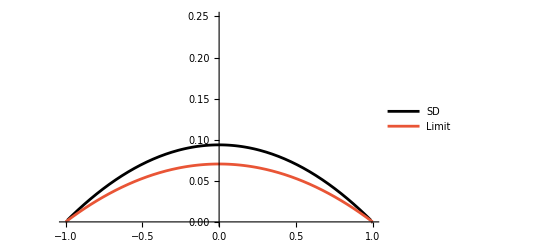

```mathematica
SDBoundaryPlot[x_,y_] = Piecewise[{{SDBoundaryPart[y],0.99<=Abs[x]<=1},{SDBoundaryPart[x],0.99<=Abs[y]<=1} }];
Show[Plot3D[SDBoundaryPlot[x,y],{x,-1,1},{y,-1,1}, BoundaryStyle->Directive[Black, Thickness[0.01]], PlotStyle->None, Mesh->None,PlotRange->{{-1,1},{-1,1},{0,1/4}}],Plot3D[SD[Abs[x],Abs[y]] ,{x,-1,1},{y,-1,1},Exclusions->None,PlotTheme->"Web"]]
Plot[{SDBoundaryPlot[x,1], SD[Abs[x],0.9999]},{x,-1,1},PlotStyle->{Black,RGBColor[0.915, 0.3325, 0.2125]}, PlotRange->{{-1,1},{0,1/4}}, PlotLegends->Placed[{"SD","Limit"},{0.9,0.7}]]
```

#### (d) Explicit SD of uniform bivariate distribution defined on a triangle

The formulas provided below were derived for a triangle with vertices at (1,0), (-1,0), and (0,√3​). A series of manual simplifications were performed to simplify the expressions, hence a step-by-step description of the process is not provided.

```mathematica
Upper[x_,y_]:=1/(1152 √3)y (32 (√3+√3 x-y)^2 y ((9 x)/(√3-y)+(24 y (-3-3 x+√3 y) ArcTanh[(3 x)/(6+3 x-2 √3 y)])/(-3+3 x^2-2 √3 x y+y^2)-(36 (-1+x) (1-Log[y]+Log[√3-√3 x+y]))/(√3-√3 x+y)-3 √3 (1+2 x-4 Log[y]+4 Log[√3-√3 x+y])-2 √3 y^2 Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))]+6 y (-1+(-1+x) Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))]))+1/y(-√3+√3 x+y)^2 ((8 (3 (1+x)^2-y^2) (-9 √3+9 √3 x^4+18 x^3 (√3-y)-y^2 (6 √3+y (-12+√3 y))+6 x (-3 √3+y (3-3 √3 y+y^2))) Log[-1+(6 (1+x))/(3+3 x-√3 y)])/(-3+3 x^2-y (2 √3+y))+1/((√3+√3 x+y) (3 (-1+x)^2-y^2))(96 y (9 √3 (-1+x) (1+x)^4-9 (1+x)^2 (-1+(-4+x) x) y-6 √3 (-2+x+4 x^2+x^3) y^2+6 (-4+(-1+x) x) y^3+√3 (5+x) y^4-y^5)-8 (3 (1+x)^2-y^2) (27+27 x^5-9 √3 y-9 x^4 (-3+√3 y)+18 x^3 (-3+2 √3 y-y^2)+y^2 (18-y (18 √3+y (-15+√3 y)))+6 x^2 (-9+y (3 √3+y (-9+√3 y)))+3 x (9+y (-12 √3+y (18-4 √3 y+y^2)))) Log[-1+(6-6 x)/(3-3 x+√3 y)]))+32 y (-√3+√3 x+y)^2 (2 y (-6-(6 (3+3 x-√3 y))/(3-3 x^2+2 √3 y+y^2)+(3 (3-3 (-2+x) x+y^2) Log[(2 y)/(√3+√3 x+y)])/(-3+3 x-√3 y))-1/(√3-y)(9-9 x+√3 y^3 Log[4]+√3 y (-9+6 x+Log[64])+y^2 (6+x Log[64])-2 y (3 x y+√3 (3+y^2)) Log[1+(3 x)/(-3+√3 y)]-6 y (√3 x+2 y) Log[2-(6 x)/(-3+3 x+√3 y)])-(12 (3 (-√3+√3 x+y)+y (-3+3 x+√3 y) Log[2-(6 x)/(-3+3 x+√3 y)]))/(3 (-1+x)^2-y^2)));
```

```mathematica
Lower[x_,y_]:=((-√3+√3 x+y)^2 √(1-2 x+x^2+y^2) (1/((-1+x)^2+y^2)4 y^2 (√3-√3 x+y) (3+x^2-2 √3 y+y^2) ((18 x (√3+√3 x-y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/((√3-y) (√3-√3 x+y)^2)+(18 x √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(3-y^2+x (-3+√3 y))+1/((√3-√3 x+y) (-3+√3 y))6 (-√3+√3 x+y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (3+√3 y Log[2]-Log[8]+(-3+√3 y) Log[√3-y]+(3-√3 y) Log[√3-√3 x-y])+√((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (-(9 x)/(√3-y)-(9 x (√3+√3 x-y)^2)/((√3-y) (√3-√3 x+y)^2)-(18 x (√3+√3 x-y))/(3-y^2+x (-3+√3 y))-(6 (√3+√3 x-y) (-√3+√3 x+y) (3+√3 y Log[2]-Log[8]+(-3+√3 y) Log[√3-y]+(3-√3 y) Log[√3-√3 x-y]))/((√3-√3 x+y) (-3+√3 y))+1/(√3-y)(-9+9 x+9 √3 y-6 √3 x y-6 y^2-6 √3 y Log[2]+12 y^2 Log[2]-6 x y^2 Log[2]-√3 y^3 Log[4]+√3 x y Log[64]-2 y (3 √3-3 √3 x-6 y+3 x y+√3 y^2) Log[√3-y]+2 y (3 √3-3 √3 x-6 y+3 x y+√3 y^2) Log[√3-√3 x-y])+1/(√3-y)6 (-√3+√3 x+y) (√3+(√3-y) (-Log[2 (√3-y)]+Log[√3-√3 x-y]))))-1/((-√3+√3 x+y) ((-1+x)^2+y^2) ((1+x)^2+y^2))9 (√3+√3 x-y)^2 (√3-√3 x+y) (1+2 x+x^2+y^2) (3+x^2-2 √3 y+y^2) (-1/(√3-√3 x+y)^3 2 (√3+√3 x-y) (-√3+√3 x+y) (-1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)-1/(√3-√3 x+y)^2 2 (-√3+√3 x+y) (-1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)-1/(√3-√3 x+y)^2 2 (-√3+√3 x+y) (1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)+(2 (-√3+√3 x+y) (1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(-3+3 x^2-2 √3 x y+y^2)-(2 (-√3+√3 x+y)^2 √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (Log[√3-√3 x-y]-Log[√3-√3 x+y]))/(3 (√3-√3 x+y))+1/(9 (-√3+√3 x+y))(√3-√3 x-y) √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) ((9 (√3-√3 x-y) (-1+x+√3 y))/(√3-√3 x+y)-(9 (√3+√3 x-y)^2 (-√3+√3 x+y) (-1+x+√3 y))/(√3-√3 x+y)^3-(18 (√3+√3 x-y) (-√3+√3 x+y) (-1+x+√3 y))/(√3-√3 x+y)^2-1/(√3-√3 x+y)6 (√3+√3 x-y) (-√3+√3 x+y)^2 (Log[√3-√3 x-y]-Log[√3-√3 x+y])+6 (-√3+√3 x+y)^2 (-Log[√3-√3 x-y]+Log[√3-√3 x+y])-(√3 (-3+6 x-3 x^2+y^2)^2 (-Log[√3-√3 x-y]+Log[√3-√3 x+y]))/(√3-√3 x+y))-1/(3 (-3+3 x^2-2 √3 x y+y^2))2 (-√3+√3 x+y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (4 √3 y+(3-3 x^2-2 √3 y+y^2) Log[√3+√3 x-y]+(-3+3 x^2+2 √3 y-y^2) Log[√3+√3 x+y])-1/9 (-√3+√3 x+y) √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (-(9 (1+x+√3 y))/(√3+√3 x-y)-(9 (√3+√3 x-y) (1+x+√3 y))/(√3-√3 x+y)^2-(18 (1+x+√3 y))/(√3-√3 x+y)+(24 √3 y-6 (-3+3 x^2+2 √3 y-y^2) Log[(√3+√3 x-y)/(√3+√3 x+y)])/(√3+√3 x-y)-(6 (-4 √3 y+(-3+3 x^2+2 √3 y-y^2) Log[(√3+√3 x-y)/(√3+√3 x+y)]))/(√3-√3 x+y)+1/(3+6 x+3 x^2-y^2)√3 (-4 √3 y (3-3 x^2+y^2)-(9 x^4+(-3+y^2)^2-6 x^2 (3+y^2)) Log[√3+√3 x-y]+(9 x^4+(-3+y^2)^2-6 x^2 (3+y^2)) Log[√3+√3 x+y])))-1/((-1+x)^2+y^2)4 y^2 (√3-√3 x+y) (3+x^2-2 √3 y+y^2) (-((18 (1+x) (√3+√3 x-y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(y (√3-√3 x+y)^2))-(18 (1+x) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(y (√3-√3 x+y))+1/(√3-√3 x+y)6 √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (2 √3+(-√3+√3 x+y) Log[2 y]-(-√3+√3 x+y) Log[√3+√3 x+y])+1/y √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (9 (1+x)+(9 (1+x) (√3+√3 x-y)^2)/(√3-√3 x+y)^2+(18 (1+x) (√3+√3 x-y))/(√3-√3 x+y)-1/(√3+√3 x+y)y^2 (-12 (√3 x+y)+(3 √3 x^2+6 x y+√3 (-3+y^2)) (-2 Log[y]+Log[1+2 x+x^2+y^2])-(3 √3 x^2+6 x y+√3 (-3+y^2)) (Log[4]-2 Log[√3+√3 x+y]+Log[(1+x)^2+y^2]))-1/(√3-√3 x+y)3 (√3+√3 x-y) y (4 √3-√3 Log[4]+√3 x Log[4]+y Log[4]+2 (-√3+√3 x+y) Log[y]-(-√3+√3 x+y) Log[3+3 x (2+x)+2 √3 y+2 √3 x y+y^2])+1/((-1+x)^2+y^2)3 (1-2 x+x^2+y^2) (-4 √3 y+y (-√3+√3 x+y) (-Log[4]-2 Log[y]+Log[3+3 x (2+x)+2 √3 y+2 √3 x y+y^2]))))+1/(12 (-1+x)^2-4 y^2)16 (√3+√3 x-y)^2 y^2 √((3+x^2-2 √3 y+y^2)/(1-2 x+x^2+y^2)) (3 √3+√3 x^2+y (-6+√3 y)) ((6 (-3+3 x+√3 y))/(√3-y)+(2 (√3+√3 x-y)^2 y (3-3 x+√3 y) Log[(2 y)/(√3-√3 x+y)])/(-3+3 x+√3 y)-((√3+√3 x-y) (3+x^2-2 √3 y+y^2) (-9 √3-9 x^2 (√3-2 y)+18 x (√3-y)+9 √3 y^2-6 y^3+2 y (6 x (√3-y) y+3 x^2 (-3+√3 y)+(-3+√3 y) (-3+y^2)) (Log[2]+Log[3]/2+Log[√3-y]-Log[3+3 x-√3 y])))/((√3-y) (-√3+√3 x+y) (3 √3+√3 x^2+y (-6+√3 y)))+6 (-√3+√3 x-y) Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))])))/(144 √3 (√3-√3 x+y) (3+x^2-2 √3 y+y^2)^(3/2));
```

```mathematica
SDpart[x_,y_]:=((-√3+√3 x+y)^2 √(1-2 x+x^2+y^2) (1/((-1+x)^2+y^2)4 y^2 (√3-√3 x+y) (3+x^2-2 √3 y+y^2) ((18 x (√3+√3 x-y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/((√3-y) (√3-√3 x+y)^2)+(18 x √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(3-y^2+x (-3+√3 y))+1/((√3-√3 x+y) (-3+√3 y))6 (-√3+√3 x+y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (3+√3 y Log[2]-Log[8]+(-3+√3 y) Log[√3-y]+(3-√3 y) Log[√3-√3 x-y])+√((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (-(9 x)/(√3-y)-(9 x (√3+√3 x-y)^2)/((√3-y) (√3-√3 x+y)^2)-(18 x (√3+√3 x-y))/(3-y^2+x (-3+√3 y))-(6 (√3+√3 x-y) (-√3+√3 x+y) (3+√3 y Log[2]-Log[8]+(-3+√3 y) Log[√3-y]+(3-√3 y) Log[√3-√3 x-y]))/((√3-√3 x+y) (-3+√3 y))+1/(√3-y)(-9+9 x+9 √3 y-6 √3 x y-6 y^2-6 √3 y Log[2]+12 y^2 Log[2]-6 x y^2 Log[2]-√3 y^3 Log[4]+√3 x y Log[64]-2 y (3 √3-3 √3 x-6 y+3 x y+√3 y^2) Log[√3-y]+2 y (3 √3-3 √3 x-6 y+3 x y+√3 y^2) Log[√3-√3 x-y])+1/(√3-y)6 (-√3+√3 x+y) (√3+(√3-y) (-Log[2 (√3-y)]+Log[√3-√3 x-y]))))-1/((-√3+√3 x+y) ((-1+x)^2+y^2) ((1+x)^2+y^2))9 (√3+√3 x-y)^2 (√3-√3 x+y) (1+2 x+x^2+y^2) (3+x^2-2 √3 y+y^2) (-1/(√3-√3 x+y)^3 2 (√3+√3 x-y) (-√3+√3 x+y) (-1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)-1/(√3-√3 x+y)^2 2 (-√3+√3 x+y) (-1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)-1/(√3-√3 x+y)^2 2 (-√3+√3 x+y) (1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2)+(2 (-√3+√3 x+y) (1+x+√3 y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(-3+3 x^2-2 √3 x y+y^2)-(2 (-√3+√3 x+y)^2 √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (Log[√3-√3 x-y]-Log[√3-√3 x+y]))/(3 (√3-√3 x+y))+1/(9 (-√3+√3 x+y))(√3-√3 x-y) √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) ((9 (√3-√3 x-y) (-1+x+√3 y))/(√3-√3 x+y)-(9 (√3+√3 x-y)^2 (-√3+√3 x+y) (-1+x+√3 y))/(√3-√3 x+y)^3-(18 (√3+√3 x-y) (-√3+√3 x+y) (-1+x+√3 y))/(√3-√3 x+y)^2-1/(√3-√3 x+y)6 (√3+√3 x-y) (-√3+√3 x+y)^2 (Log[√3-√3 x-y]-Log[√3-√3 x+y])+6 (-√3+√3 x+y)^2 (-Log[√3-√3 x-y]+Log[√3-√3 x+y])-(√3 (-3+6 x-3 x^2+y^2)^2 (-Log[√3-√3 x-y]+Log[√3-√3 x+y]))/(√3-√3 x+y))-1/(3 (-3+3 x^2-2 √3 x y+y^2))2 (-√3+√3 x+y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (4 √3 y+(3-3 x^2-2 √3 y+y^2) Log[√3+√3 x-y]+(-3+3 x^2+2 √3 y-y^2) Log[√3+√3 x+y])-1/9 (-√3+√3 x+y) √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (-(9 (1+x+√3 y))/(√3+√3 x-y)-(9 (√3+√3 x-y) (1+x+√3 y))/(√3-√3 x+y)^2-(18 (1+x+√3 y))/(√3-√3 x+y)+(24 √3 y-6 (-3+3 x^2+2 √3 y-y^2) Log[(√3+√3 x-y)/(√3+√3 x+y)])/(√3+√3 x-y)-(6 (-4 √3 y+(-3+3 x^2+2 √3 y-y^2) Log[(√3+√3 x-y)/(√3+√3 x+y)]))/(√3-√3 x+y)+1/(3+6 x+3 x^2-y^2)√3 (-4 √3 y (3-3 x^2+y^2)-(9 x^4+(-3+y^2)^2-6 x^2 (3+y^2)) Log[√3+√3 x-y]+(9 x^4+(-3+y^2)^2-6 x^2 (3+y^2)) Log[√3+√3 x+y])))-1/((-1+x)^2+y^2)4 y^2 (√3-√3 x+y) (3+x^2-2 √3 y+y^2) (-((18 (1+x) (√3+√3 x-y) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(y (√3-√3 x+y)^2))-(18 (1+x) √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2))/(y (√3-√3 x+y))+1/(√3-√3 x+y)6 √((1-2 x+x^2+y^2)/(3+x^2-2 √3 y+y^2)) (3 √3+√3 x^2-6 y+√3 y^2) (2 √3+(-√3+√3 x+y) Log[2 y]-(-√3+√3 x+y) Log[√3+√3 x+y])+1/y √((1-2 x+x^2+y^2) (3+x^2-2 √3 y+y^2)) (9 (1+x)+(9 (1+x) (√3+√3 x-y)^2)/(√3-√3 x+y)^2+(18 (1+x) (√3+√3 x-y))/(√3-√3 x+y)-1/(√3+√3 x+y)y^2 (-12 (√3 x+y)+(3 √3 x^2+6 x y+√3 (-3+y^2)) (-2 Log[y]+Log[1+2 x+x^2+y^2])-(3 √3 x^2+6 x y+√3 (-3+y^2)) (Log[4]-2 Log[√3+√3 x+y]+Log[(1+x)^2+y^2]))-1/(√3-√3 x+y)3 (√3+√3 x-y) y (4 √3-√3 Log[4]+√3 x Log[4]+y Log[4]+2 (-√3+√3 x+y) Log[y]-(-√3+√3 x+y) Log[3+3 x (2+x)+2 √3 y+2 √3 x y+y^2])+1/((-1+x)^2+y^2)3 (1-2 x+x^2+y^2) (-4 √3 y+y (-√3+√3 x+y) (-Log[4]-2 Log[y]+Log[3+3 x (2+x)+2 √3 y+2 √3 x y+y^2]))))+1/(12 (-1+x)^2-4 y^2)16 (√3+√3 x-y)^2 y^2 √((3+x^2-2 √3 y+y^2)/(1-2 x+x^2+y^2)) (3 √3+√3 x^2+y (-6+√3 y)) ((6 (-3+3 x+√3 y))/(√3-y)+(2 (√3+√3 x-y)^2 y (3-3 x+√3 y) Log[(2 y)/(√3-√3 x+y)])/(-3+3 x+√3 y)-((√3+√3 x-y) (3+x^2-2 √3 y+y^2) (-9 √3-9 x^2 (√3-2 y)+18 x (√3-y)+9 √3 y^2-6 y^3+2 y (6 x (√3-y) y+3 x^2 (-3+√3 y)+(-3+√3 y) (-3+y^2)) (Log[2]+Log[3]/2+Log[√3-y]-Log[3+3 x-√3 y])))/((√3-y) (-√3+√3 x+y) (3 √3+√3 x^2+y (-6+√3 y)))+6 (-√3+√3 x-y) Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))])))/(144 √3 (√3-√3 x+y) (3+x^2-2 √3 y+y^2)^(3/2))+1/(1152 √3)y (32 (√3+√3 x-y)^2 y ((9 x)/(√3-y)+(24 y (-3-3 x+√3 y) ArcTanh[(3 x)/(6+3 x-2 √3 y)])/(-3+3 x^2-2 √3 x y+y^2)-(36 (-1+x) (1-Log[y]+Log[√3-√3 x+y]))/(√3-√3 x+y)-3 √3 (1+2 x-4 Log[y]+4 Log[√3-√3 x+y])-2 √3 y^2 Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))]+6 y (-1+(-1+x) Log[((√3+√3 x-y) y)/(3-y^2+x (-3+√3 y))]))+1/y(-√3+√3 x+y)^2 ((8 (3 (1+x)^2-y^2) (-9 √3+9 √3 x^4+18 x^3 (√3-y)-y^2 (6 √3+y (-12+√3 y))+6 x (-3 √3+y (3-3 √3 y+y^2))) Log[-1+(6 (1+x))/(3+3 x-√3 y)])/(-3+3 x^2-y (2 √3+y))+1/((√3+√3 x+y) (3 (-1+x)^2-y^2))(96 y (9 √3 (-1+x) (1+x)^4-9 (1+x)^2 (-1+(-4+x) x) y-6 √3 (-2+x+4 x^2+x^3) y^2+6 (-4+(-1+x) x) y^3+√3 (5+x) y^4-y^5)-8 (3 (1+x)^2-y^2) (27+27 x^5-9 √3 y-9 x^4 (-3+√3 y)+18 x^3 (-3+2 √3 y-y^2)+y^2 (18-y (18 √3+y (-15+√3 y)))+6 x^2 (-9+y (3 √3+y (-9+√3 y)))+3 x (9+y (-12 √3+y (18-4 √3 y+y^2)))) Log[-1+(6-6 x)/(3-3 x+√3 y)]))+32 y (-√3+√3 x+y)^2 (2 y (-6-(6 (3+3 x-√3 y))/(3-3 x^2+2 √3 y+y^2)+(3 (3-3 (-2+x) x+y^2) Log[(2 y)/(√3+√3 x+y)])/(-3+3 x-√3 y))-1/(√3-y)(9-9 x+√3 y^3 Log[4]+√3 y (-9+6 x+Log[64])+y^2 (6+x Log[64])-2 y (3 x y+√3 (3+y^2)) Log[1+(3 x)/(-3+√3 y)]-6 y (√3 x+2 y) Log[2-(6 x)/(-3+3 x+√3 y)])-1/(3 (-1+x)^2-y^2)12 (3 (-√3+√3 x+y)+y (-3+3 x+√3 y) Log[2-(6 x)/(-3+3 x+√3 y)])))
```

Using axial symmetries of a triangle we obtain the exact SD of the  uniform distribution on the triangle with vertices (1,0), (-1,0),(0,√3).

```mathematica
SD[x_,y_]:=Piecewise[{{SDpart[Abs[x],y],-1<x<1&&0<y<((1-Abs[x])/√3)},{SDpart[Abs[1/2 (1-x-√3 y)],1/2 (√3+√3 x-y)],0<=Abs[1/2 (1-x-√3 y)]<1&&0<1/2 (√3+√3 x-y)<=((1-Abs[1/2 (1-x-√3 y)])/√3)},{SDpart[Abs[1/2 (-1-x+√3 y)],1/2 (√3-√3 x-y)],0<Abs[1/2 (-1-x+√3 y)]<1&&0<1/2 (√3-√3 x-y)<((1-Abs[1/2 (-1-x+√3 y)])/√3)}}];
```

```mathematica
Plot3D[SD[x,y],{x,-1,1},{y,0,(1-Abs[x]) √3},ColorFunction->"SolarColors",Exclusions->None,PlotRange->Full,PlotPoints->50]
```

-Graphics3D-

### (e) Application: Numerical approximation of Sylvester probability on triangle

```mathematica
1-4*6/Sqrt[3]*NIntegrate[SDpart[x,y],{x,0,1},{y,0,(1-x)/ √3}]
```

0.666667

### (f) Application: Exact SD in the centroid of a triangle

```mathematica
Simplify[SDpart[0,Sqrt[3]/3]]
```

2/81 (3+Log[1024])

### (g) Algorithm: Explicit SD of uniform bivariate distribution defined on a convex polygon

A supplementary intersect function is designed to compute the intersection point of a line and a line segment in a two-dimensional plane.
Input :
L1: A list of two points that define a line. Each point is represented as a list of two coordinates.
L2: A list of two points that define a line segment. Each point is represented as a list of two coordinates.
Output:
If the line and the line segment do not intersect, the function returns an empty set.
If they do intersect, the function returns the coordinates of the intersection point.

```mathematica
Intersect[L1_,L2_]:=Graphics`Mesh`FindIntersections[{InfiniteLine[L1],Line[L2]}]
```

The functions I1, I2, and I3 are defined in Theorem 5 of the main paper. The primitive functions of the integrals involved in these definitions are detailed in  Appendix B.

```mathematica
I1[γ_, δ_, c_]:=-Cot[δ+c]+Cot[γ+c]
I2[γ_,δ_,a_,b_,c_]:=-Sin[b-a]*Log[Abs[1+Tan[b-c]/Tan[δ+c]]]/Sin[b-c]^2 - Sin[a-c]/Sin[b-c]*1/Tan[δ + c]+Sin[b-a]*Log[Abs[1+Tan[b-c]/Tan[γ+c]]]/Sin[b-c]^2 + Sin[a-c]/Sin[b-c]*1/Tan[γ + c]
I3[γ_,δ_,a_,b_,c_]:=-2Sin[a-c]*Sin[b-a]/Sin[b-c]^3 *Log[Abs[1+Tan[b-c]/Tan[δ + c]]]- Sin[a-c]^2 /Sin[b-c]^2 * 1/Tan[δ+c]-(Sin[b-a]^2)/ (Cos[b-c]^2 * Sin[b-c]^2) * 1/(Tan[δ + c] + Tan[b-c]) -(-2Sin[a-c]*Sin[b-a]/Sin[b-c]^3 *Log[Abs[1+Tan[b-c]/Tan[γ+ c]]]- Sin[a-c]^2 /Sin[b-c]^2 * 1/Tan[γ+c]-(Sin[b-a]^2)/ (Cos[b-c]^2 * Sin[b-c]^2) * 1/(Tan[γ + c] + Tan[b-c]) )
```

Function to calculate exact SD of a polygon. For details see Theorem 5 in the main paper. 
Input :
x1: An x-coordinate of point whose simplicial depth is to be calculated.
x2: An y-coordinate of point whose simplicial depth is to be calculated.
Y: A list of angularly sorted vertices of a convex polygon. Each point is represented as a list of two coordinates.
P: A convex hull of vertices in Y (Polygon[Y]). 
Output:
Exact simplicial depth of point (x1,x2) with respect to uniform distribution defined on convex polygon induced by vertices in Y.

```mathematica
exactSD[x1_,x2_,Y_,P_]:=Module[{x,y,intersection,Su,Sl,theta,tau,psi,count,u,el,r,s,alfa,beta,a,b,su,sl,S,atilde,btilde,cF,cG,SD},
If[!RegionMember[P,{x1,x2}],Return[0]];
y=Y;
x ={x1,x2};
Do[y[[i]] = (y[[i]]-x), {i, 1,Length[y]}];
y=-SortBy[-y,ArcTan@@#&];
intersection = {};
Do[intersection = Union[intersection, Intersect[{y[[1]], -y[[1]]},{y[[i]],y[[i+1]]}] ],{i, 2,Length[y]-1}];
AppendTo[y, intersection[[1]]];
y=-SortBy[-y,ArcTan@@#&];
Su = {};
j=1;Until[y[[j]]==intersection[[1]], AppendTo[Su,y[[j]]];j++];
Clear[j];
Sl = -SortBy[-SymmetricDifference[y,Su],ArcTan@@#&];
k = Length[Su];
m = Length[y];
theta = {0};
tau = {0};
Do[AppendTo[tau, ArcCos[Dot[y[[j]],y[[1]]]/(Norm[y[[j]]]*Norm[y[[1]]])]],{j,2,k}];
Do[AppendTo[theta, ArcCos[Dot[y[[j]],y[[1]]]/(Norm[y[[j]]]*Norm[y[[1]]])]],{j,2,k}];
AppendTo[tau,π];
psi = {0};
Do[AppendTo[psi, ArcCos[Dot[-y[[j+k]],y[[1]]]/(Norm[-y[[j+k]]]*Norm[y[[1]]])]],{j,2,m-k}];
Do[AppendTo[theta, ArcCos[Dot[-y[[j+k]],y[[1]]]/(Norm[-y[[j+k]]]*Norm[y[[1]]])]],{j,2,m-k}];
AppendTo[psi,π];
theta = Sort[theta];
AppendTo[theta,π];
count=0;
u={};
Do[
Do[
If[tau[[i]]<=theta[[j]], count=count+1],
{i,1,k}];
AppendTo[u, count];
count=0,
 {j, 1, m}]
el={};
Do[
Do[
If[psi[[i]]<=theta[[j]], count=count+1],
{i,1,m-k}];
AppendTo[el, count];
count=0,
 {j, 1, m}]
r = {};
Do[AppendTo[r,Norm[y[[j]]]],{j,1,k}]
s = {};
Do[AppendTo[s,Norm[y[[j+k]]]],{j,1,m-k}]
alfa = {};
Do[AppendTo[alfa, Angle[{0,0},y[[j]],y[[j+1]]]],{j, 1, k}]
beta = {};
Do[AppendTo[beta, Angle[{0,0},y[[j+k]],y[[j+k+1]]]],{j, 1, m-k-1}]
AppendTo[beta, Angle[{0,0},y[[m]],y[[1]]]];
a={};
Do[AppendTo[a, r[[j]]^2 *Sin[alfa[[j]]]*Sin[tau[[j+1]]-tau[[j]]]/(2*Sin[alfa[[j]]+tau[[j+1]]-tau[[j]]])],{j,1,k}]
b={};
Do[AppendTo[b, s[[j]]^2 *Sin[beta[[j]]]*Sin[psi[[j+1]]-psi[[j]]]/(2*Sin[beta[[j]]+psi[[j+1]]-psi[[j]]])],{j,1,m-k}]
su = Sum[a[[j]], {j,1,k}];
sl = Sum[b[[j]], {j,1,m-k}];
S = su+sl;
atilde = {};
btilde = {};
Do[AppendTo[atilde, 1/su * Sum[a[[i]], {i,1,u[[j]]-1}]],{j,1,m}]
Do[AppendTo[btilde, 1/sl * Sum[b[[i]], {i,1,el[[j]]-1}]],{j,1,m}]
cF={};
cG={};
Do[AppendTo[cF, r[[u[[j]]]]^2 *Sin[alfa[[u[[j]]]]]/(2*su)],{j,1,m}]
Do[AppendTo[cG, s[[el[[j]]]]^2 *Sin[beta[[el[[j]]]]]/(2*sl)],{j,1,m}]
SD= Simplify[6*su^2 *sl / S^3 *Sum[cG[[j]]*Sin[beta[[el[[j]]]]](atilde[[j]]*(1-atilde[[j]])*I1[theta[[j]], theta[[j+1]], beta[[el[[j]]]]- psi[[el[[j]]]]] + cF[[j]]*(1-2*atilde[[j]])*I2[theta[[j]], theta[[j+1]],-tau[[u[[j]]]],alfa[[u[[j]]]]-tau[[u[[j]]]] , beta[[el[[j]]]]- psi[[el[[j]]]]] - cF[[j]]^2 * I3[theta[[j]], theta[[j+1]],-tau[[u[[j]]]],alfa[[u[[j]]]]-tau[[u[[j]]]] , beta[[el[[j]]]]- psi[[el[[j]]]]]),{j,1,m-1}] + 6*sl^2 *su / S^3 *Sum[cF[[j]]*Sin[alfa[[u[[j]]]]](btilde[[j]]*(1-btilde[[j]])*I1[theta[[j]], theta[[j+1]], alfa[[u[[j]]]]-tau[[u[[j]]]]] + cG[[j]]*(1-2*btilde[[j]])*I2[theta[[j]], theta[[j+1]],- psi[[el[[j]]]],beta[[el[[j]]]]- psi[[el[[j]]]] , alfa[[u[[j]]]]-tau[[u[[j]]]]] - cG[[j]]^2 * I3[theta[[j]], theta[[j+1]],- psi[[el[[j]]]],beta[[el[[j]]]]- psi[[el[[j]]]] , alfa[[u[[j]]]]-tau[[u[[j]]]]]),{j,1,m-1}] ];
Return[SD];
]
```

3D plotting function of  exact SD of a polygon.
Input :
Y: A list of angularly sorted vertices of a convex polygon. 
Output:
3D plot of exact SD of uniform distribution defined on convex polygon induced by vertices in Y.

```mathematica
plotSD[Y_]:=Module[{Y3D, ymax, xmax,ymin,xmin},
Y3D=Y;
Do[AppendTo[Y3D[[i]],0],{i,Length[Y]}];
xmax = Max[First/@Y]+0.1;
ymax = Max[Last/@Y]+0.1;
xmin= Min[First/@Y]-0.1;
ymin = Min[Last/@Y]-0.1;
Return[Show[Plot3D[{exactSD[x1,x2,Y,Polygon[Y]]},{x1,xmin,xmax},{x2,ymin,ymax},PlotPoints->70,Exclusions->None,PlotTheme->"Web",PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SolarColors"][z]]],Graphics3D[{EdgeForm[Directive[Black,Thickness[0.001]]],FaceForm[White],Polygon[{{xmin,ymin,0},{xmax,ymin,0},{xmax,ymax,0},{xmin,ymax,0}}]}],Graphics3D[{EdgeForm[Directive[White,Thickness[0.015]]],FaceForm[],Polygon[Y3D]}]]];]
```

Contour plotting function of  exact SD of a polygon.
Input :
Y: A list of  angularly sorted vertices of a convex polygon. 
Output:
Contour plot of exact SD of uniform distribution defined on convex polygon induced by vertices in Y.

```mathematica
contourSD[Y_]:=Module[{ymax, xmax,ymin,xmin},
xmax = Max[First/@Y]+0.1;
ymax = Max[Last/@Y]+0.1;
xmin= Min[First/@Y]-0.1;
ymin = Min[Last/@Y]-0.1;
Return[Show[ContourPlot[exactSD[x1,x2,Y,Polygon[Y]],{x1,xmin,xmax},{x2,ymin,ymax },ColorFunction->"SolarColors",PlotLegends->Automatic,PlotRange->All,PlotPoints->40],Graphics[{EdgeForm[Directive[White,Thickness[0.01]]],FaceForm[],Polygon[Y]}]]];]
```

#### Examples

(i) Pentagon

-Graphics3D-

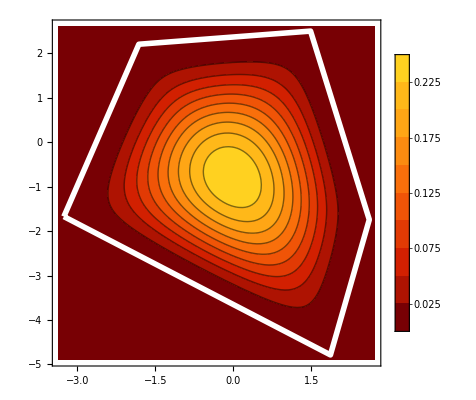

```mathematica
Y={{-3.2614062259877494,-1.6726424531789208},{1.8675622131558196,-4.784796184049087},{2.6151745619123385,-1.7421877879469703},{1.4850628719315528,2.500077632903981},{-1.818340529550745,2.204509960139776}};
plotSD[Y]
contourSD[Y]
```

(ii) Octagon

-Graphics3D-

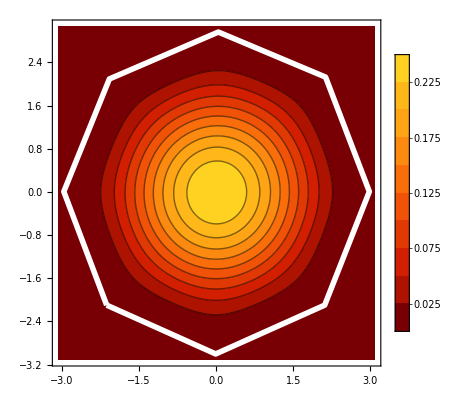

```mathematica
Y={{-2.1312945360069633,-2.0980457196472124},{-0.010161825581487705,-3.0021350716318405},{2.1109708848439883,-2.0980457196472124},{2.9802875694445934,0.005700657086251726},{2.128357218536001,2.126833367511727},{0.041997175494548955,2.961377384728308},{-2.0791355349309266,2.092060700127703},{-2.965838553223543,0.005700657086251726}};
plotSD[Y]
contourSD[Y]
```

(iii) Trapezoid

-Graphics3D-

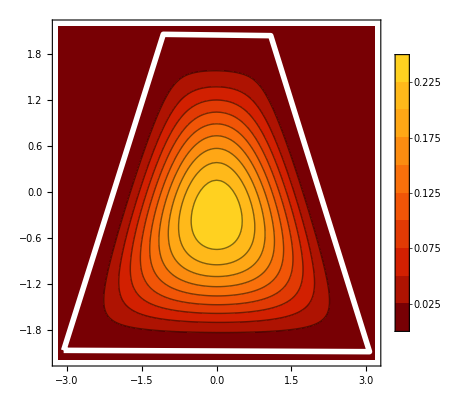

```mathematica
Y = {{-3.0701565553756156,-2.0632730522631886},{3.067219237904654,-2.0806593859551996},{1.085177197015276,2.0399016990516667},{-1.0707281807942257,2.057288032743679}};
plotSD[Y]
contourSD[Y]
```

### (h) Algorithm: Explicit SD of uniform bivariate distribution defined on a boundary of a convex polygon (extra material not included in the thesis)

Function to calculate exact SD of a uniform distribution supported on a boundary of a polygon. 
Input :
x1: An x-coordinate of point whose simplicial depth is to be calculated.
x2: An y-coordinate of point whose simplicial depth is to be calculated.
Y: A list of angularly sorted vertices of a convex polygon. Each point is represented as a list of two coordinates.
P: A convex hull of vertices in Y (Polygon[Y]). 
Output:
Exact simplicial depth of point (x1,x2) with respect to uniform distribution defined on a boundary of the convex polygon induced by the vertices in Y.

```mathematica
boundarySD[x1_,x2_,Y_,P_]:=Module[{x,y,intersection,Su,Sl,theta,tau,psi,count,u,el,r,s,alfa,beta,a,b,su,sl,S,atilde,btilde,cF,cG,SD},
If[!RegionMember[P,{x1,x2}],Return[0]];
y=Y;
x ={x1,x2};
Do[y[[i]] = (y[[i]]-x), {i, 1,Length[y]}];
y=-SortBy[-y,ArcTan@@#&];
intersection = {};
Do[intersection = Union[intersection, Intersect[{y[[1]], -y[[1]]},{y[[i]],y[[i+1]]}] ],{i, 2,Length[y]-1}];
AppendTo[y, intersection[[1]]];
y=-SortBy[-y,ArcTan@@#&];
Su = {};
j=1;Until[y[[j]]==intersection[[1]], AppendTo[Su,y[[j]]];j++];
Clear[j];
Sl = -SortBy[-SymmetricDifference[y,Su],ArcTan@@#&];
k = Length[Su];
m = Length[y];
theta = {0};
tau = {0};
Do[AppendTo[tau, ArcCos[Dot[y[[j]],y[[1]]]/(Norm[y[[j]]]*Norm[y[[1]]])]],{j,2,k}];
Do[AppendTo[theta, ArcCos[Dot[y[[j]],y[[1]]]/(Norm[y[[j]]]*Norm[y[[1]]])]],{j,2,k}];
AppendTo[tau,π];
psi = {0};
Do[AppendTo[psi, ArcCos[Dot[-y[[j+k]],y[[1]]]/(Norm[-y[[j+k]]]*Norm[y[[1]]])]],{j,2,m-k}];
Do[AppendTo[theta, ArcCos[Dot[-y[[j+k]],y[[1]]]/(Norm[-y[[j+k]]]*Norm[y[[1]]])]],{j,2,m-k}];
AppendTo[psi,π];
theta = Sort[theta];
AppendTo[theta,π];
count=0;
u={};
Do[
Do[
If[tau[[i]]<=theta[[j]], count=count+1],
{i,1,k}];
AppendTo[u, count];
count=0,
 {j, 1, m}]
el={};
Do[
Do[
If[psi[[i]]<=theta[[j]], count=count+1],
{i,1,m-k}];
AppendTo[el, count];
count=0,
 {j, 1, m}]
r = {};
Do[AppendTo[r,Norm[y[[j]]]],{j,1,k}]
s = {};
Do[AppendTo[s,Norm[y[[j+k]]]],{j,1,m-k}]
alfa = {};
Do[AppendTo[alfa, Angle[{0,0},y[[j]],y[[j+1]]]],{j, 1, k}]
beta = {};
Do[AppendTo[beta, Angle[{0,0},y[[j+k]],y[[j+k+1]]]],{j, 1, m-k-1}]
AppendTo[beta, Angle[{0,0},y[[m]],y[[1]]]];
a={};
Do[AppendTo[a, r[[j]] *Sin[tau[[j+1]]-tau[[j]]]/Sin[alfa[[j]]+tau[[j+1]]-tau[[j]]]],{j,1,k}]
b={};
Do[AppendTo[b, s[[j]] *Sin[psi[[j+1]]-psi[[j]]]/Sin[beta[[j]]+psi[[j+1]]-psi[[j]]]],{j,1,m-k}]
su = Sum[a[[j]], {j,1,k}];
sl = Sum[b[[j]], {j,1,m-k}];
S = su+sl;
atilde = {};
btilde = {};
Do[AppendTo[atilde, 1/su * Sum[a[[i]], {i,1,u[[j]]-1}]],{j,1,m}]
Do[AppendTo[btilde, 1/sl * Sum[b[[i]], {i,1,el[[j]]-1}]],{j,1,m}]
cF={};
cG={};
Do[AppendTo[cF, r[[u[[j]]]]/su],{j,1,m}]
Do[AppendTo[cG, s[[el[[j]]]]/sl],{j,1,m}]
SD= Simplify[6*su^2 *sl / S^3 *Sum[cG[[j]]*Sin[beta[[el[[j]]]]](atilde[[j]]*(1-atilde[[j]])*I1[theta[[j]], theta[[j+1]], beta[[el[[j]]]]- psi[[el[[j]]]]] + cF[[j]]*(1-2*atilde[[j]])*I2[theta[[j]], theta[[j+1]],-tau[[u[[j]]]],alfa[[u[[j]]]]-tau[[u[[j]]]] , beta[[el[[j]]]]- psi[[el[[j]]]]] - cF[[j]]^2 * I3[theta[[j]], theta[[j+1]],-tau[[u[[j]]]],alfa[[u[[j]]]]-tau[[u[[j]]]] , beta[[el[[j]]]]- psi[[el[[j]]]]]),{j,1,m-1}] + 6*sl^2 *su / S^3 *Sum[cF[[j]]*Sin[alfa[[u[[j]]]]](btilde[[j]]*(1-btilde[[j]])*I1[theta[[j]], theta[[j+1]], alfa[[u[[j]]]]-tau[[u[[j]]]]] + cG[[j]]*(1-2*btilde[[j]])*I2[theta[[j]], theta[[j+1]],- psi[[el[[j]]]],beta[[el[[j]]]]- psi[[el[[j]]]] , alfa[[u[[j]]]]-tau[[u[[j]]]]] - cG[[j]]^2 * I3[theta[[j]], theta[[j+1]],- psi[[el[[j]]]],beta[[el[[j]]]]- psi[[el[[j]]]] , alfa[[u[[j]]]]-tau[[u[[j]]]]]),{j,1,m-1}] ];
Return[SD];
]
```

Plotting functions for boundarySD.

```mathematica
plotSDb[Y_]:=Module[{Y3D, ymax, xmax,ymin,xmin},
Y3D=Y;
Do[AppendTo[Y3D[[i]],0],{i,Length[Y]}];
xmax = Max[First/@Y]+0.1;
ymax = Max[Last/@Y]+0.1;
xmin= Min[First/@Y]-0.1;
ymin = Min[Last/@Y]-0.1;
Return[Show[Plot3D[{boundarySD[x1,x2,Y,Polygon[Y]]},{x1,xmin,xmax},{x2,ymin,ymax},PlotPoints->70,PlotTheme->"Web",Exclusions->None,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SolarColors"][z]]],Graphics3D[{EdgeForm[Directive[Black,Thickness[0.001]]],FaceForm[White],Polygon[{{xmin,ymin,0},{xmax,ymin,0},{xmax,ymax,0},{xmin,ymax,0}}]}],Graphics3D[{EdgeForm[Directive[White,Thickness[0.015]]],FaceForm[],Polygon[Y3D]}]]];]
```

```mathematica
contourSDb[Y_]:=Module[{ymax, xmax,ymin,xmin},
xmax = Max[First/@Y]+0.1;
ymax = Max[Last/@Y]+0.1;
xmin= Min[First/@Y]-0.1;
ymin = Min[Last/@Y]-0.1;
Return[Show[ContourPlot[boundarySD[x1,x2,Y,Polygon[Y]],{x1,xmin,xmax},{x2,ymin,ymax },ColorFunction->"SolarColors",PlotLegends->Automatic,PlotRange->All,PlotPoints->40],Graphics[{EdgeForm[Directive[White,Thickness[0.01]]],FaceForm[],Polygon[Y]}]]];]
```

#### Examples

(i) Triangle (boundary)

```mathematica
Y={{0.2506331797986947,2.724058265210232},{-2.844134217379459,-1.7616158273288887},{2.0761982174599645,-3.413317528070037}};
plotSDb[Y]
```

-Graphics3D-

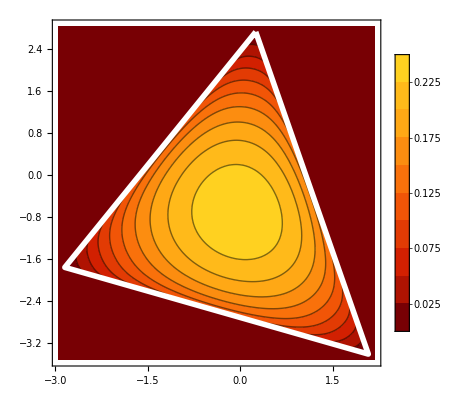

```mathematica
contourSDb[Y]
```

(ii) Trapezoid (boundary)

-Graphics3D-

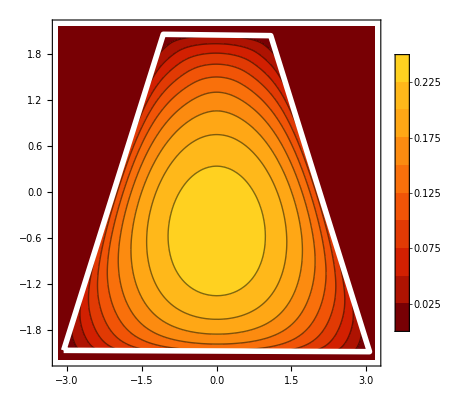

```mathematica
Y = {{-3.0701565553756156,-2.0632730522631886},{3.067219237904654,-2.0806593859551996},{1.085177197015276,2.0399016990516667},{-1.0707281807942257,2.057288032743679}};
plotSDb[Y]
contourSDb[Y]
```

(iii) Pentagon (boundary)

-Graphics3D-

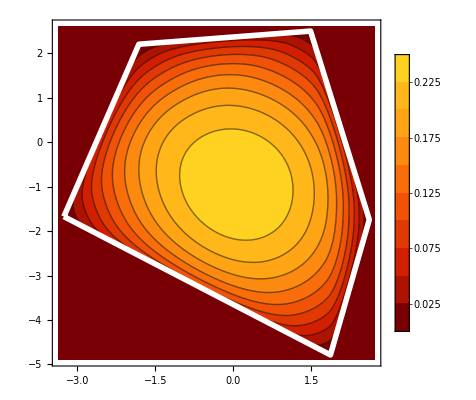

```mathematica
Y={{-3.2614062259877494,-1.6726424531789208},{1.8675622131558196,-4.784796184049087},{2.6151745619123385,-1.7421877879469703},{1.4850628719315528,2.500077632903981},{-1.818340529550745,2.204509960139776}};
plotSDb[Y]
contourSDb[Y]
```

(iv) Octagon (boundary)

-Graphics3D-

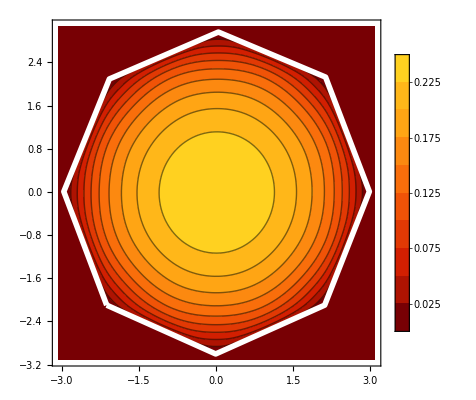

```mathematica
Y={{-2.1312945360069633,-2.0980457196472124},{-0.010161825581487705,-3.0021350716318405},{2.1109708848439883,-2.0980457196472124},{2.9802875694445934,0.005700657086251726},{2.128357218536001,2.126833367511727},{0.041997175494548955,2.961377384728308},{-2.0791355349309266,2.092060700127703},{-2.965838553223543,0.005700657086251726}};
plotSDb[Y]
contourSDb[Y]
```

For more examples click on the grid to select polygon vertices. Make sure the vertices are in convex position. The chosen vertices will be stored in the variable Y. To plot the exact SD for your chosen polygon, execute the code below the grid.

```mathematica
Y={};
DynamicModule[{},EventHandler[Dynamic@Graphics[{Point[Dynamic[Y]],Red,PointSize[Large],Dynamic@Point@MousePosition["Graphics"],Gray,Line[{{#,-5},{#,5}}]&/@Range[-5,5],Line[{{-5,#},{5,#}}]&/@Range[-5,5]},PlotRange->{{-5,5},{-5,5}},Frame->True],{"MouseClicked":>(AppendTo[Y,MousePosition["Graphics"]])}],Initialization:>(Y={})]
```

-Graphics3D-

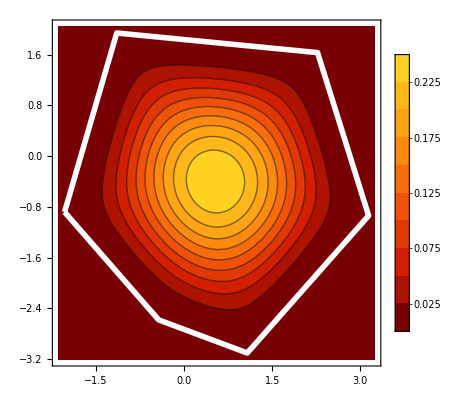

-Graphics3D-

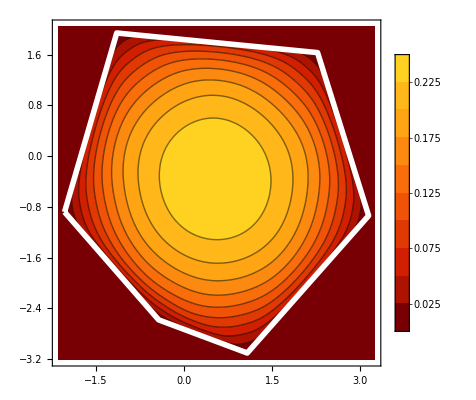

```mathematica
Y= SortBy[Y,ArcTan@@(#-Mean[Y])&];
plotSD[Y]
contourSD[Y]
plotSDb[Y]
contourSDb[Y]
```